# Portfolio Maximization

## Basic Return/Volatility Statistic

For a given portfolio, we can calculate the following quantity:

S(p)=(R_t(p))/(σ_t(p))

Where p is some portfolio, S is the statistic we want to calculate, R is the annualized return of the portfolio based on the data from time t, and σ is the volatility of a portfolio based on the data from time t.
So the “Best” portfolio would be p such that S is maximum, that is, the portfolio that gives the BEST return to volatility ratio.

## Altered Statistic.

One thing I don’t like is that it allows for 0’s in the denominator. And it does not allow for priority. Maybe I want to opt for a safer or less safe portfolio depending on the situation. It also makes it non-intuitive on how to add new factors you might want to take into consideration. Let’s address each of these issues.

### Zeroes

To avoid zeroes, we’ll wrap each quantity in a modified sigmoid (Σ(x)), this makes it so the values always stay between 0.5 and 1.5. Greater values will give a greater out put, so it still gives more weight to high values (in other words, the function is monotonic.

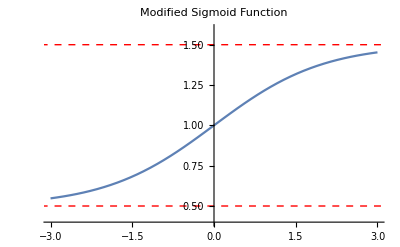

Notice that ratios that were greater before are not necessarily greater now. That is:

a_1/b_1>a_2/b_2  DOES NOT IMPLY   (Σ(a_1))/(Σ(b_1))>(Σ(a_2))/(Σ(b_2))

### Priority and more factors.

Now that we have the zeroes issue out of the way, one way we can put in a priority system for our quantities is by raising them to a power. Since positive values are always greater then one (due to Σ), they will always increase when raised to a positive power. And similarly for negative quantities. So out new statistic now looks like.

S(p)=Σ[R_t(p)]^α/Σ[σ_t(p)]^β

Where α and β are the ‘weights’ I want to put on the return and volatility (respectivelly).
But wait... Remember that we’re trying to find the p that gives me the maximum S. But that same p would give the same as if it was the maximum of some other monotonic function of S, say... natural log? and now we can use those nice property of logarithms to make this way simpler (another reason now to have zeros). Lets define ℒ(x)=ln(Σ(x)). So.

Ln(S(p))=αℒ(R_t(p))-βℒ(σ_t(p))

Now look at that, I can simply set the weights. And now nothing can stop us from looking at other parameters to shove in this statistic to be maximized.

## Time Dependend Statistic

Something that bothers me is this. Say my program is gonna analyze the data every hour, calculate the best portfolio, and trade accordingly. Ok, but how far back do I analyze data? a month? a week? 2 hours? What is the best Δt/tratio? What about the older data? Can I maybe analyze both but somehow give more priority newer data vs older and.... oh wait, I totally can! Let’s do it like this!

Ln(S(p))=w_T_1 ℒ(R_T_1(p))+w_T_2 ℒ(R_T_2(p))+...-v_T_1 ℒ(σ_T_1(p))-v_T_2 ℒ(σ_T_2(p))

Where w_T_1,w_T_2...are the weights given for each of the times for the returns, and v_T_1,v_T_2... is the same for the volatilities. Notice that they don’t need to add up to 1, since I can simply have more priority on returns then weights or vice versa.
Cool let’s make this nice and pretty

Ln(S(p))=∑_(t=t_0)^T w_t ℒ(R_t(p))-∑_(t=t_0)^T v_t ℒ(R_t(p))8p

Now that’s a lot of parameters... We can surerly run some backtests and find the BEST parameters (for whatever measure of best you want)

```mathematica
Show[
Plot[1/(1+ⅇ^-x)+1/2,{x,-3,3},PlotRange->{{-3,3},{0.4,1.6}},PlotLabel->"Modified Sigmoid Function"],
Graphics[{
{Dashed,Red,InfiniteLine[{{0,1.5},{1,1.5}}]},
{Dashed,Red,InfiniteLine[{{0,0.5},{1,0.5}}]},

}]
]
```

-Graphics-

```mathematica
{}
```